```mathematica
n=20;

angles=Join[{0,Pi/2},Table[ArcTan[1/Sqrt[k]],{k,1,n-1}]];

pts=AnglePath[angles];
```

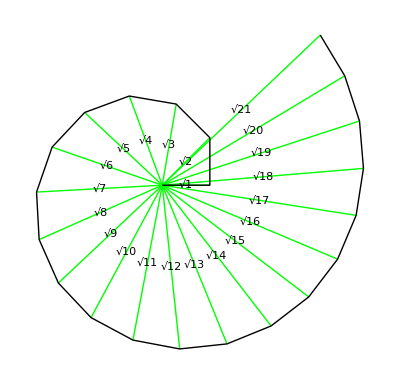

```mathematica
Graphics[{Green,Line[{#,{0,0}}&/@pts],Black,Thick,Line[pts],MapIndexed[Text[DisplayForm[SqrtBox[First[#2]]],Mean[{#1,{0,0}}],BaseStyle->Blue]&,pts[[2;;]]]}]
```